```mathematica
Chaotic controller simulation

(*largest lyapunov exponent
x(t) = f^t(x_0)
x(t) + \delta(t) = f^t(x_0 + \delta x_0)
sensitivity of initial conditions:
||\delta x(t)|| = ||\delta x_0||e^{\mu t}
log(||\frac{\delta x(t)}{||\delta x_0||}||) = \mu t
*)

(*Boost needs higher output precision so that 1e-8 is visible in the data*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
i=6
j=39

unperturbedChaoticController = Import["creature2/log["<>ToString[i] <>"]PitchChaoticController.tsv","Data"];
(*unperturbedChaoticController = Import["unperturbed-walk/log[0]PitchJointModel.tsv","Data"];*)
unperturbedLength = Length[unperturbedChaoticController];

glessWalk = Import["g-less-movement/log["<>ToString[i] <>"]PitchChaoticController.tsv","Data"];

(*perturbedChaoticController = Import["walk"<>ToString[j] <>"/log["<>ToString[i] <>"]PitchChaoticController.tsv","Data"];

(*perturbedChaoticController = Import["walk2/log[0]PitchJointModel.tsv","Data"];*)
perturbedLength=Length[perturbedChaoticController];

(*dx0 = {1*10^-8,1*10^-8,1*10^-8};*)
dx0 = perturbedChaoticController[[1]] - unperturbedChaoticController[[1]]; (*\delta x_0, the initial perturbation*)

dxt=perturbedChaoticController - unperturbedChaoticController; (*\deltax(t) of the whole trajectory*)

normdxt = {}; (*norms of the \delta x(t)s*)

Do[normdxt=Append[normdxt,Norm[dxt[[i]]]],{i,1,unperturbedLength}]; (* Calculate all norms *)

lambdats= Log[normdxt/Norm[dx0]]; (* The lyapunov exponents multiplied by the time steps t *)

lces=Rest[Re[lambdats]];(*/Range[unperturbedLength-1];*) (* lyapunov characteristic exponents *)
lces;
Max[lces] (* Maximunm lyapunov exponent *)
line=Fit[lces,{1,x},x]*)

Show[ListPointPlot3D[{unperturbedChaoticController}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend["Test",LabelStyle->{GrayLevel[0.3],18}]],Graphics3D[Line[{unperturbedChaoticController}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}] 

ListLinePlot[Drop[lces,-3000],ImageSize->1400,Axes->True,AxesLabel->{"t","Lyapunov exponents"},PlotRange->All]


(*Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[jointMovementTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400] *)

(*lces=Rest[FoldList[Plus,0,Re[Log[mut]]]]/Range[K];*)
```

6

39

Thread::tdlen: Objects of unequal length in {{-0.285412, 0.174607, 0.0274097}, {0.467126, -0.337744, 0.0260071}, {0.465914, -0.290926, 0.0287202}, {0.464941, -0.233423, 0.0310572}, {0.464246, -0.16675, 0.0329321}, « 42 », {0.469377, 0.557557, 0.0288328}, {0.471939, 0.614713, 0.0243523}, {0.474651, 0.651021, 0.0194126}, « 4750 »} + {{« 1 »}, « 49 », « 18291 »} cannot be combined.

Part::partw: Part 3 of {{-0.285412, 0.174607, 0.0274097}, {0.467126, -0.337744, 0.0260071}, {0.465914, -0.290926, 0.0287202}, {0.464941, -0.233423, 0.0310572}, {0.464246, -0.16675, 0.0329321}, « 42 », {0.469377, 0.557557, 0.0288328}, {0.471939, 0.614713, 0.0243523}, {0.474651, 0.651021, 0.0194126}, « 4750 »} + {{« 1 »}, « 49 », « 18291 »} does not exist.

Part::partw: Part 4 of {{-0.285412, 0.174607, 0.0274097}, {0.467126, -0.337744, 0.0260071}, {0.465914, -0.290926, 0.0287202}, {0.464941, -0.233423, 0.0310572}, {0.464246, -0.16675, 0.0329321}, « 42 », {0.469377, 0.557557, 0.0288328}, {0.471939, 0.614713, 0.0243523}, {0.474651, 0.651021, 0.0194126}, « 4750 »} + {{« 1 »}, « 49 », « 18291 »} does not exist.

Part::partw: Part 5 of {{-0.285412, 0.174607, 0.0274097}, {0.467126, -0.337744, 0.0260071}, {0.465914, -0.290926, 0.0287202}, {0.464941, -0.233423, 0.0310572}, {0.464246, -0.16675, 0.0329321}, « 42 », {0.469377, 0.557557, 0.0288328}, {0.471939, 0.614713, 0.0243523}, {0.474651, 0.651021, 0.0194126}, « 4750 »} + {{« 1 »}, « 49 », « 18291 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
1
```

0

1

20.5333

-Graphics3D-

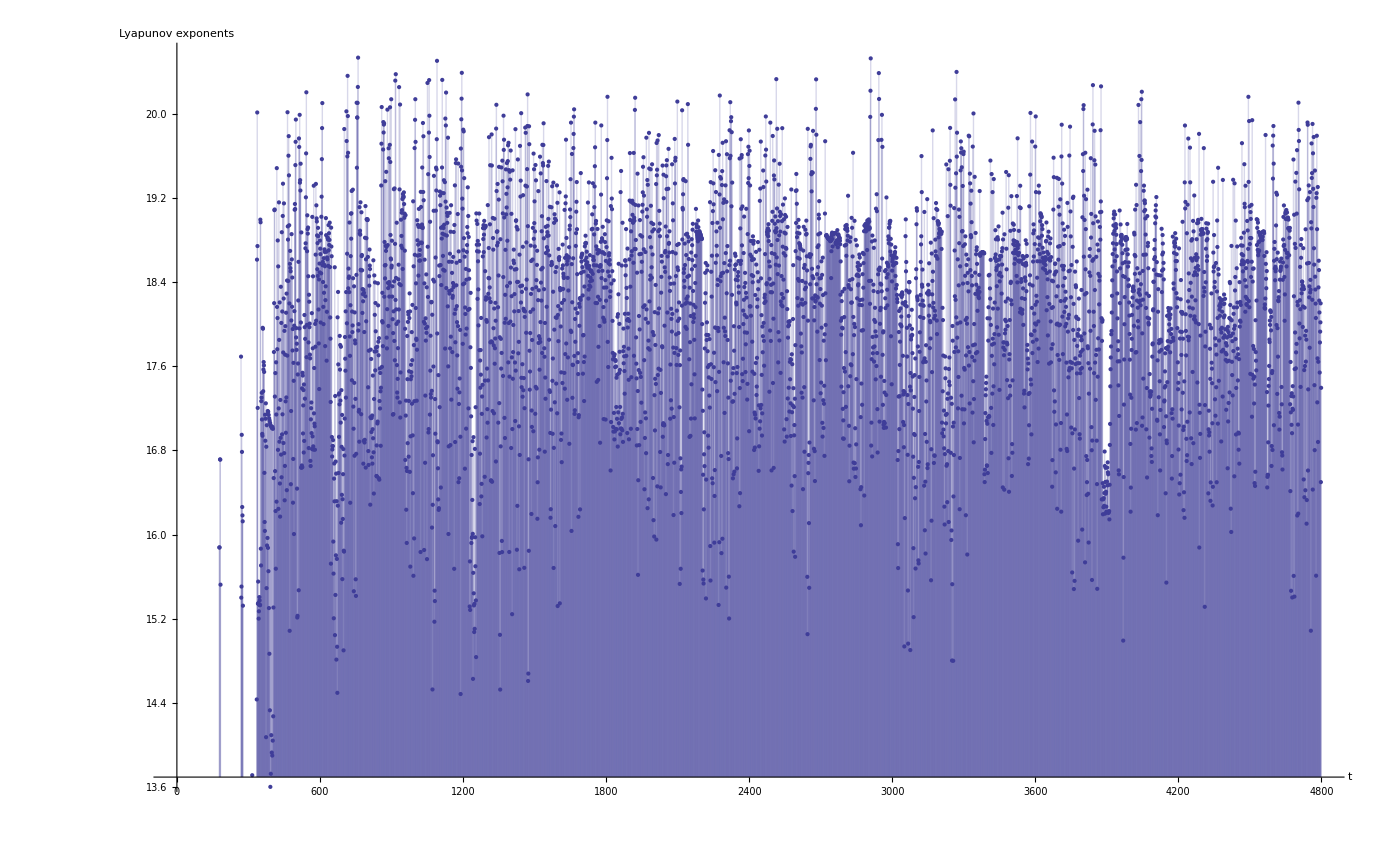

```mathematica
SetDirectory[NotebookDirectory[]];
i=0
j=1

unperturbedChaoticController = Import["unperturbed-walk/log[0]PitchJointModel.tsv","Data"];
(*unperturbedChaoticController = Import["unperturbed-walk/log[0]PitchJointModel.tsv","Data"];*)
unperturbedLength = Length[unperturbedChaoticController];

(*perturbedChaoticController = Import["walk"<>ToString[j] <>"/log["<>ToString[i] <>"]PitchChaoticController.tsv","Data"];*)

perturbedChaoticController = Import["walk"<>ToString[j] <>"/log["<>ToString[i] <>"]PitchJointModel.tsv","Data"];
perturbedLength=Length[perturbedChaoticController];

(*dx0 = {1*10^-8,1*10^-8,1*10^-8};*)
dx0 = perturbedChaoticController[[1]] - unperturbedChaoticController[[1]]; (*\delta x_0, the initial perturbation*)

dxt=perturbedChaoticController - unperturbedChaoticController; (*\deltax(t) of the whole trajectory*)

normdxt = {}; (*norms of the \delta x(t)s*)

Do[normdxt=Append[normdxt,Norm[dxt[[i]]]],{i,1,unperturbedLength}]; (* Calculate all norms *)

lambdats= Log[normdxt/Norm[dx0]]; (* The lyapunov exponents multiplied by the time steps t *)

lces=Rest[Re[lambdats]];(*/Range[unperturbedLength-1];*) (* lyapunov characteristic exponents *)
lces;
Max[lces] (* Maximunm lyapunov exponent *)

Show[ListPointPlot3D[{unperturbedChaoticController,perturbedChaoticController}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend["Test",LabelStyle->{GrayLevel[0.3],18}]],Graphics3D[Line[{unperturbedChaoticController,perturbedChaoticController}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}] 

ListPlot[lces,Filling->Axis,ImageSize->1400,Axes->True,AxesLabel->{"t","Lyapunov exponents"}]
```